```mathematica
CloseKernels[];
LaunchKernels[16];
```

### Definitions

```mathematica
ClearAll[f,g,makeTestData];
f[{i_,j_,k_},{x_,y_,z_},{w_,h_,d_}]:=Boole[x<=i<x+w&&y≤j<y+h&&z≤k<z+d];

g[{i_,j_,k_},{min_,max_}]:=N[
min + 
(*Diag*)
Sum[
(max-min)*(k/100)*f[{i,j,k},{s,s,s},{10,10,10}],
{s,1,100,10}] + 
(*Corners*)
(max-min)*(i/100)*f[{i,j,k},{11,1,1},{90,10,10}]+
(max-min)*(j/100)*f[{i,j,k},{1,11,1},{10,90,10}]+
(max-min)*(k/100)*f[{i,j,k},{1,1,11},{10,10,90}]+
(max-min)*(i/100)*f[{i,j,k},{80,80,1},{20,20,20}]+
(max-min)*(k/100)*f[{i,j,k},{80,1,80},{20,20,20}]+
(max-min)*(j/100)*f[{i,j,k},{1,80,80},{20,20,20}]];

makeTestData[{min_,max_}]:=ParallelTable[
g[{i,j,k},{min,max}],
{i,1,100},{j,1,100},{k,1,100}];
```

```mathematica
formats={
{"UINT8","UnsignedInteger8",0,2^8-1},
{"UINT16","UnsignedInteger16",0,2^16-1},
{"UINT32","UnsignedInteger32",0,2^32-1},
(*{"UINT64","UnsignedInteger64",0,2^64-1}, not in opengl*)
{"INT8","Integer8",-2^7,2^7-1},
{"INT16","Integer16",-2^15,2^15-1},
{"INT32","Integer32",-2^31,2^31-1},
(*{"INT64","Integer64",-2^63,2^63-1}, Not in opengl *)
(*{"FLOAT16","Real16",0,1}, Not in mathematica... *)
{"FLOAT32","Real32",0,1}
(* {"FLOAT64","Real64",0,1} not in opengl *)
};
```

```mathematica
writeTestData[path_,filename_,data_,format_,binformat_,range_]:=Module[{datdata,fun=Identity},
datdata = "Rawfile: <file>
Resolution: <dim>
Format: <format>
BasisVector1: 1.0 0.0 0.0
BasisVector2: 0.0 1.0 0.0
BasisVector3: 0.0 0.0 1.0
DataRange: <datarange>
ValueRange: 0 1
ValueUnit: arb. unit";

If[StringMatchQ[format,___~~"INT"~~___],fun =Floor];

Print@Export[FileNameJoin[{path,filename<>".raw"}],fun[Flatten[data]],{"Binary",binformat}];
Print@Export[FileNameJoin[{path,filename<>".dat"}],StringReplace[datdata,{
"<file>"->filename<>".raw","<dim>"->StringJoin[Riffle[ToString/@Dimensions[data]," "]],
"<format>" ->format,
"<datarange>" ->StringJoin[Riffle[ToString/@range," "]]}],"String"];
];
```

```mathematica
path="/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets";
```

### Debug

```mathematica
test = makeTestData[{0,255}];
Image3D[test]
```

-Graphics3D-

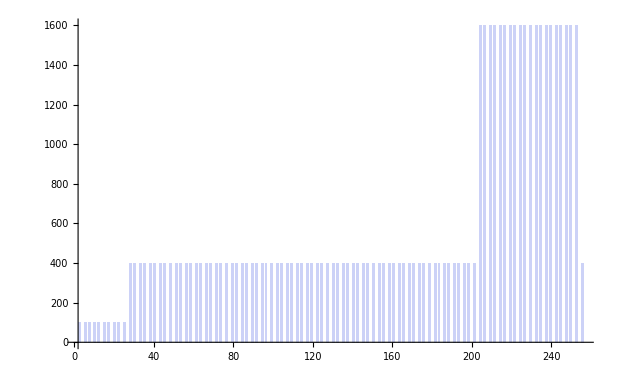

```mathematica
Histogram[Cases[Flatten[test],x_/;x≠0],{1}]
```

### Generate test data over the whole data range

```mathematica
Do[
Print[format];
range = {format[[3]],format[[4]]};
test = makeTestData[range];
writeTestData[path,"testdata.defaultRange."<>format[[1]]<>"",test,format[[1]],format[[2]],range];
,{format,formats[[All]]}
]
```

### Generate test data over [0, random max]

```mathematica
newRanges = Table[
If[StringMatchQ[format[[1]],___~~"INT"~~___],
{0,RandomInteger[{1,format[[4]]}]}
,
{0,RandomReal[{0,10000}]}
],{format,formats}]
```

{{0,36},{0,36216},{0,3083760888},{0,71},{0,3105},{0,1749215716},{0,935.776}}

```mathematica
newRanges={{0,163},{0,8619},{0,3278719337},{0,37},{0,1470},{0,2082936410},{0,3599.1841125361225}};

Do[
format=formats[[i]];
range=newRanges[[i]];
Print[format];
Print[range];
test = makeTestData[range];
writeTestData[path,"testdata.zeroToMax."<>format[[1]]<>"",test,format[[1]],format[[2]],range];
,{i,1,Length[formats]}
]
```

### Generate test data over [random min > 0, random max]

```mathematica
newRanges = Table[
If[StringMatchQ[format[[1]],___~~"INT"~~___],
 Sort[RandomInteger[Clip[{format[[3]],format[[4]]},{0,format[[4]]}],{2}]]
,
Sort[RandomReal[{0,10000},{2}]]
],{format,formats}]
```

```mathematica
newRanges = {{60,204},{968,18949},{1318008542,2614229896},{5,84},{3203,27260},{1375143796,1521510916},{7393.9521826161035,7448.0341081759725}};

Do[
format=formats[[i]];
range=newRanges[[i]];
Print[format];
Print[range];
test = makeTestData[range];
writeTestData[path,"testdata.posMinToMax."<>format[[1]]<>"",test,format[[1]],format[[2]],range];
,{i,1,Length[formats]}
]
```

### Generate test data over [random min < 0 (0 for unsigned), random max]

```mathematica
newRanges = Table[
If[StringMatchQ[format[[1]],___~~"INT"~~___],
 Sort[RandomInteger[Clip[{format[[3]],format[[4]]},{format[[3]],format[[4]]}],{2}]]
,
{RandomReal[{-10000,0}],RandomReal[{0,10000}]}
],{format,formats}]
```

```mathematica
newRanges ={{84,151},{17638,27008},{3368296324,4082875550},{-121,49},{-24762,8392},{-1763534432,1578523303},{-7659.491871958435,2467.530164069396}};

Do[
format=formats[[i]];
range=newRanges[[i]];
Print[format];
Print[range];
test = makeTestData[range];
writeTestData[path,"testdata.negMinToMax."<>format[[1]]<>"",test,format[[1]],format[[2]],range];
,{i,1,Length[formats]}
]
```

### Generate test data over [random min < 0 (0 for unsigned), random max < 0 (>0 for unsigned)]

```mathematica
newRanges = Table[
If[StringMatchQ[format[[1]],___~~"UINT"~~___],
 Sort[RandomInteger[Clip[{format[[3]],format[[4]]},{format[[3]],format[[4]]}],{2}]]
,
If[StringMatchQ[format[[1]],___~~"INT"~~___],
Sort[RandomInteger[Clip[{format[[3]],format[[4]]},{format[[3]],0}],{2}]]
,
Sort[RandomReal[{-10000,0},{2}]]
]
],{format,formats}]
```

```mathematica
newRanges ={{93,186},{25099,25766},{46722623,1844173066},{-59,-18},{-11322,-10385},{-1919154727,-1616767855},{-9765.027134014808,-5882.440922856933}};

Do[
format=formats[[i]];
range=newRanges[[i]];
Print[format];
Print[range];
test = makeTestData[range];
writeTestData[path,"testdata.negMinToNegMax."<>format[[1]]<>"",test,format[[1]],format[[2]],range];
,{i,1,Length[formats]}
]
```